```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Needs["PolygonPlotMarkers`"]
```

```mathematica
shapes=PolygonMarker[All];
shapesTip=Table[
Tooltip[Graphics[{FaceForm[pltcolors[[i]]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[shapes[[i]],Scaled[.3]]},ImageSize->15],shapes[[i]]],
{i,1,Length@pltcolors}]
shapesTipTable={shapesTip,
Table[i,{i,1,Length@pltcolors}]}//Transpose
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,7},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,13},{-Graphics-,14},{-Graphics-,15}}

```mathematica
pltmarkers={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
?dataPltNBeamsPlt
```

Plot dispersion relation for discrete beams; Arguments are dataPltNBeamsPlt[gList_,thetaList_,numrange_:{-8.9,8.9},numstep_:0.09,pltRange_:{{-5,5},{-5,5}}]

## Play with Raffelt’s Example

Plot the function ω(n),

The degeneracy is hidden: The second and third solutions overlap with each other.

```mathematica
eigenValuesAsIndexRaffelt=Table[
Table[
{nM,
Eigenvalues[
nMatFunNBeams[{-0.5/(2Pi),0.5/(2Pi)},nM,{ArcCos@0.9,ArcCos[0.3]}]
][[i]]},
{i,1,4}],
{nM,-5,5,0.009}
]//Transpose;
```

```mathematica
listpltOmegan1=ListPlot[
eigenValuesAsIndexRaffelt,
Frame->True,ImageSize->Large,PlotStyle->pltcolors,PlotMarkers->pltmarkers,PlotLegends->Automatic,FrameLabel->{"n","ω"}
]
Manipulate[
Show[%,PlotRange->{Automatic,{-pltrg,pltrg}}],
{pltrg,
{4,10,20}
},SaveDefinitions->True]
```

```mathematica
(*Export["export/listpltOmegan1.png",listpltOmegan1]*)
```

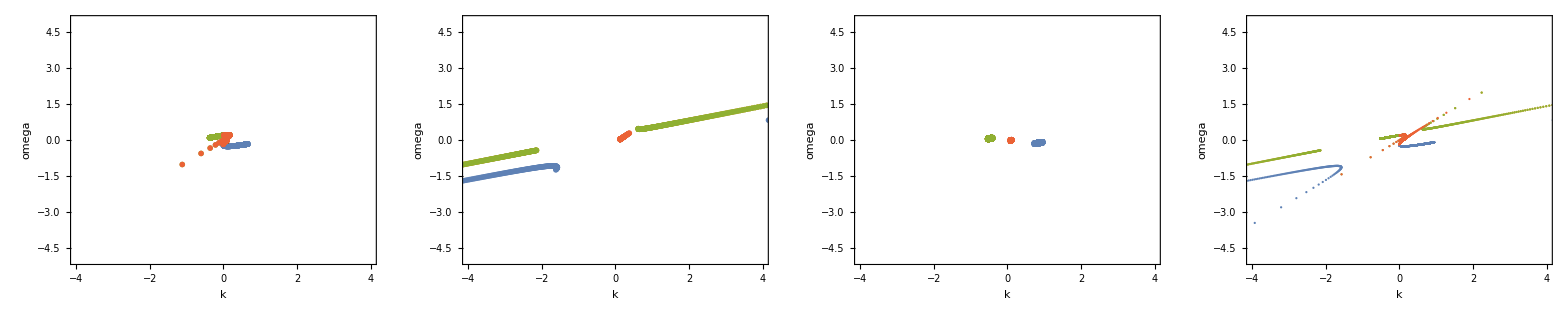

```mathematica
listpltDispersionRelationDecompose1=Grid@
{{
dataPltNBeamsPlt[{-0.5/(2Pi),0.5/(2Pi)},{ArcCos@0.9,ArcCos[0.3]},{-4,1.1},0.009,{{-3.99,3.99},{-5,5}}],
dataPltNBeamsPlt[{-0.5/(2Pi),0.5/(2Pi)},{ArcCos@0.9,ArcCos[0.3]},{1.3,5},0.009,{{-3.99,3.99},{-5,5}}],
dataPltNBeamsPlt[{-0.5/(2Pi),0.5/(2Pi)},{ArcCos@0.9,ArcCos[0.3]},{-10,-5},0.009,{{-3.99,3.99},{-5,5}}],
dataPltNBeamsPlt[{-0.5/(2Pi),0.5/(2Pi)},{ArcCos@0.9,ArcCos[0.3]},{-9.9,5},0.009,{{-3.99,3.99},{-5,5}}]
}}
```

```mathematica
Export["export/listpltDispersionRelationDecompose1-0.9-0.3.png",listpltDispersionRelationDecompose1]
```

export/listpltDispersionRelationDecompose1-0.9-0.3.png

```mathematica
nMatFunNBeams[{1,1,1,1,1,1},0.2,{ArcCos@0.9,ArcCos[0.8],ArcCos@0.7,ArcCos[0.5],ArcCos[0.4],ArcCos[0.3]}]
```

{{-31.7273,0.,0.,-17.6883},{0.,10.253,0.,0.},{0.,0.,10.253,0.},{17.6883,0.,0.,11.2212}}

```mathematica
pltDiffBeams[beams_]:=dataPltNBeamsPlt[
Join[Table[-1/beams/(2Pi),{n,1,beams/2}],Table[1/beams/(2Pi),{n,1,beams/2}]],
Table[ArcCos@0.9+n(ArcCos@0.3-ArcCos@0.9)/(beams-1),{n,0,beams-1}],{-10,10},0.0049,{{-10,10},{-10,10}}]
```

```mathematica
listanimi1=ListAnimate[
Table[
Show[pltDiffBeams[beams],PlotRange->{{-6,6},{-4,4}},PlotLabel->"Beams:"<>ToString@beams]
,{beams,{2,6,8,10,20,50,100,200}}
],(*AnimationRunning->False,*)Deployed->True
]
```

$Aborted

```mathematica
Export["export/listanimi1.avi",listanimi1]
```

export/listanimi1.avi

```mathematica
ArcCos@0.9
ArcCos@0.3
ArcCos@0.3-ArcCos@0.9
Pi/3//N
Pi/3+Pi/4//N
```

0.451027

1.2661

0.815077

1.0472

1.8326

```mathematica
pltDataOk=
Table[

Table[
Table[{
k,k Cos@Table[ArcCos@0.9+n (ArcCos@0.3-ArcCos@0.9)/(beams-1),{n,0,beams-1}][[i]]
}
,{i,1,beams}],
{k,-200,200,0.9}],
{beams,{4}}]//First//Transpose;
```

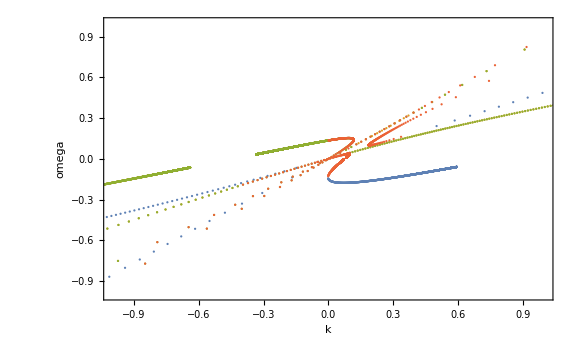

```mathematica
Show[pltDiffBeams[4],ImageSize->Large,PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
Manipulate[
Show[ListPlot[pltDataOk,Frame->True,Joined->True,PlotStyle->Yellow],pltDiffBeams[4],ImageSize->Large,PlotRange->{{-range,range},{-range,range}}],
{range,0,30}]
```

ListPlot::lpn: pltDataOk is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ListPlot[pltDataOk, Frame → True, Joined → True, PlotStyle → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[1, 1, 0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.6666666666666666`, 0.6666666666666666`, 0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

ListPlot::lpn: pltDataOk is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ListPlot[pltDataOk, Frame → True, Joined → True, PlotStyle → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[1, 1, 0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.6666666666666666`, 0.6666666666666666`, 0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

```mathematica
?nMatFunNBeams
```

Calculate N matrix in z direction for discrete beams; Arguments are nMatFunNBeams[gList_,nIndex_,thetaList_]

```mathematica
eigenValuesEx1[beams_]:=
Table[
Table[
{nM,
Eigenvalues[
nMatFunNBeams[Join[Table[-1/beams/(2Pi),{n,1,beams/2}],Table[1/beams/(2Pi),{n,1,beams/2}]],nM,
Table[ArcCos@0.9+n (ArcCos@0.3-ArcCos@0.9)/(beams-1),{n,0,beams-1}]]
][[i]]},
{i,1,4}],
{nM,-10,10,0.009}
]//Transpose
```

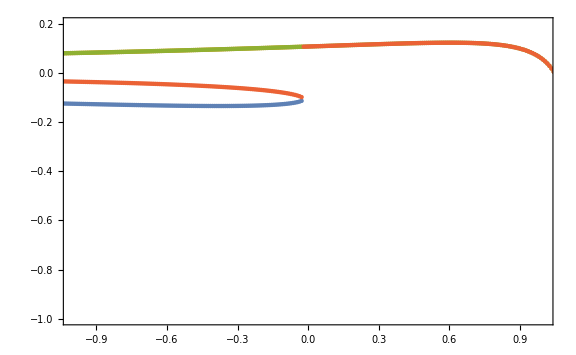

```mathematica
ListPlot[
eigenValuesEx1[100],
Frame->True,ImageSize->Large,PlotRange->{{-1,1},{-1,0.2}}]
```

```mathematica
Table[
ListPlot[
eigenValuesEx1[beams],
Frame->True,ImageSize->Large,PlotLegends->Automatic,FrameLabel->{"n","ω"},PlotLabel->"Beams: "<>ToString@beams,PlotMarkers->{""}
],
{beams,{6}}]
```

{-Graphics-}

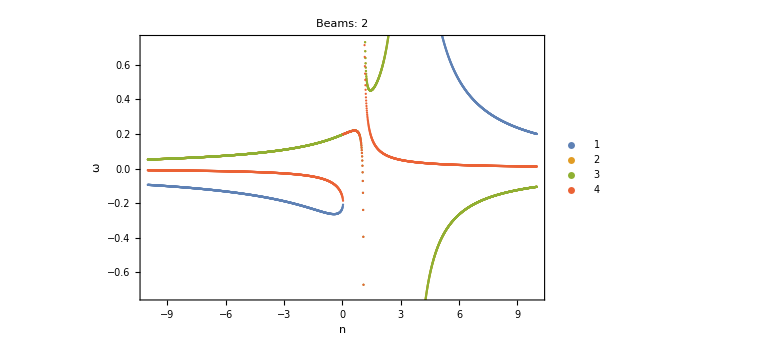
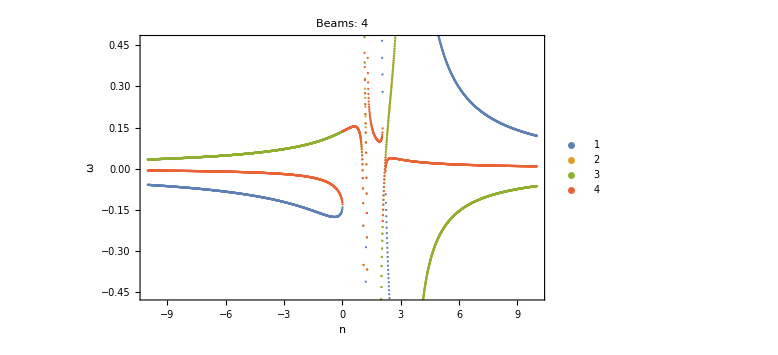
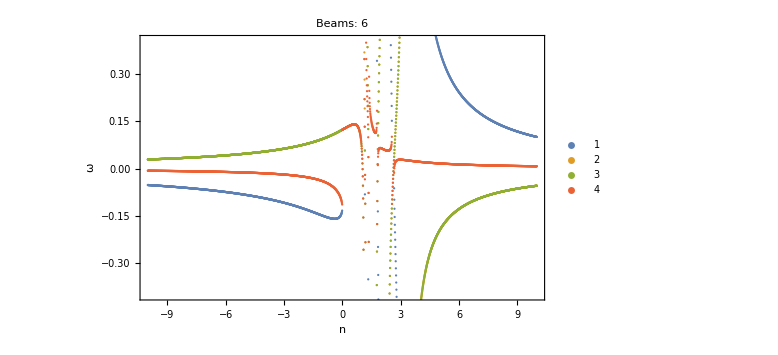
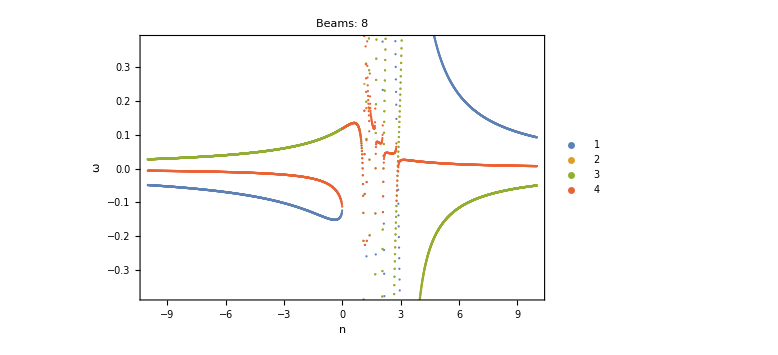
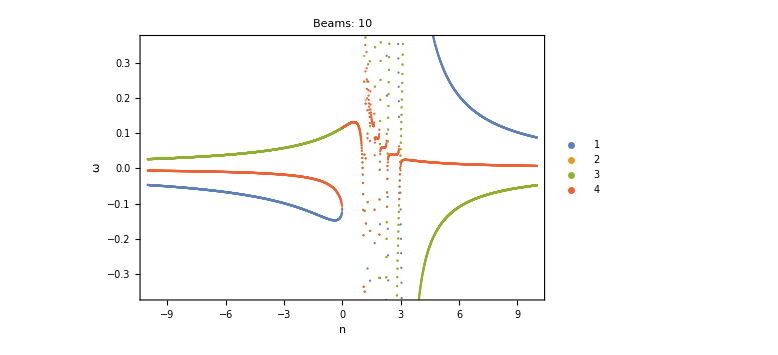

```mathematica
listpltOmegan12List=Table[
ListPlot[
eigenValuesEx1[beams],
Frame->True,ImageSize->Large,PlotLegends->Automatic,FrameLabel->{"n","ω"},PlotLabel->"Beams: "<>ToString@beams
],
{beams,{2,4,6,8,10}}]
```

```mathematica
Table[
Export["export/listpltOmegan12List-"<>ToString[2 i]<>".png",listpltOmegan12List[[i]]],
{i,1,5}]
```

{export/listpltOmegan12List-2.png,export/listpltOmegan12List-4.png,export/listpltOmegan12List-6.png,export/listpltOmegan12List-8.png,export/listpltOmegan12List-10.png}

```mathematica
pltDiffBeamsConfined[beams_]:=dataPltNBeamsPlt[
Join[Table[-1/beams/(2Pi),{n,1,beams/2}],Table[1/beams/(2Pi),{n,1,beams/2}]],
Table[Pi/3+n Pi/2/(beams-1),{n,0,beams-1}],{-1,1},0.049,{{-10,10},{-10,10}}]
```

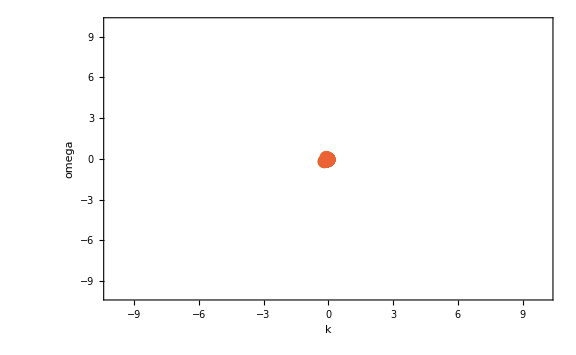

```mathematica
pltDiffBeamsConfined[10]
```

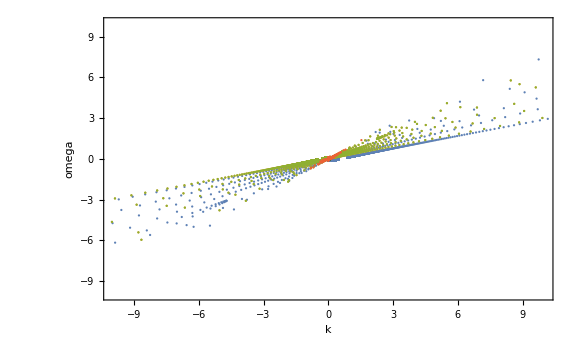

```mathematica
pltDiffBeams[10]
```

```mathematica
(*Export["export/pltDiffBeamsConfined-n-in--1-to-1-beams-10.png",pltDiffBeamsConfined[10]]*)
```

```mathematica
pltdataCont=Import["export/pltdata-continuous-beams.csv"];
```

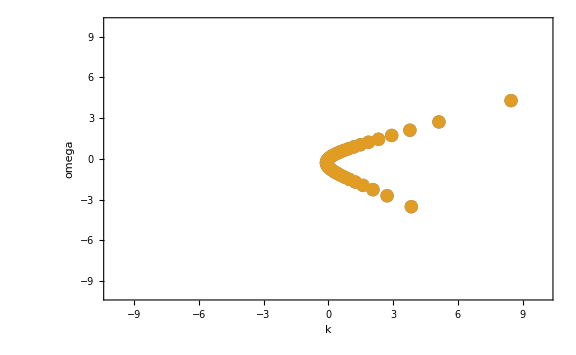

```mathematica
listpltCont=ListPlot[ToExpression@pltdataCont,Joined->False,Frame->True,ImageSize->Large,PlotRange->{{-10,10},{-10,10}},FrameLabel->{"k","omega"}]
```

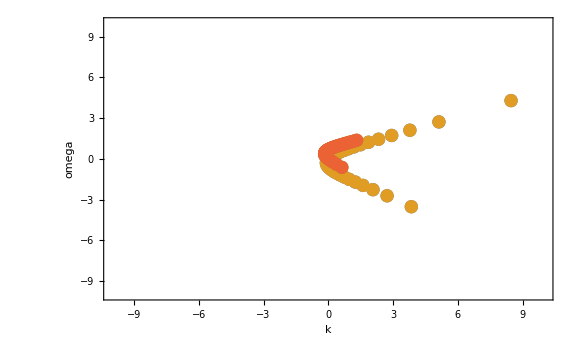

$Aborted

```mathematica
Show[listpltCont,pltDiffBeamsConfined[4]]
(*Export["export/compare-continuous-and-10-beams-within-n-range--1-to-1.png",%]*)
```